```mathematica
NS["schizo_testresults_8moments"]
```

```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\nanunana\\data_schizo_bins170802"]
```

C:\Users\pglpm\repositories\nanunana\data_schizo_bins170802

```mathematica
quantities={"weights","weighteddegree","normweighteddegree","clustcoeff"};
```

```mathematica
Do[binsc=Import[ii<>"_Control","Table"];binss=Import[ii<>"_Schizo","Table"];
plot=ListPlot[{Mean@T[binsc],Mean@T[binss]},Joined->True,PlotRange->All,PlotLabel->mylabels[{ii}]];expdfr["histmeans_"<>ii,plot],{ii,quantities}];
```

```mathematica
Do[binsc=Import[ii<>"_Control","Table"];binss=Import[ii<>"_Schizo","Table"];
plot=ListPlot[Join[T[binsc],T[binss]],PlotStyle->Join[Table[{Opacity[0.25],bpurple},Length@T@binsc],Table[{Opacity[0.25],red},Length@T@binss]],
Joined->True,PlotRange->All,PlotLabel->mylabels[{ii}]];expdfr["histall_"<>ii,plot],{ii,quantities}];
```

```mathematica
Do[binsc=Import[ii<>"_Control","Table"];binss=Import[ii<>"_Schizo","Table"];
plot=ListPlot[Join[T[binsc],T[binss],{Mean@T[binsc],Mean@T[binss]}],PlotStyle->Join[Table[{Opacity[0.25],bpurple},Length@T@binsc],Table[{Opacity[0.25],red},Length@T@binss],{{Opacity[1],bpurple,Thick},{Opacity[1],red,Thick}}],
Joined->True,PlotRange->All,PlotLabel->mylabels[{ii}]];expdfr["histallm_"<>ii,plot],{ii,quantities}];
```

```mathematica
binsc=Import["weights_Control","Table"];binss=Import["weights_Schizo","Table"];
```

```mathematica
Dimensions[bins]
```

{120,56}

```mathematica
Array[a,{2,3}]-Array[b,2]
```

{{a[1,1]-b[1],a[1,2]-b[1],a[1,3]-b[1]},{a[2,1]-b[2],a[2,2]-b[2],a[2,3]-b[2]}}

```mathematica
Std@T[binsc-Mean@T@binsc];
```

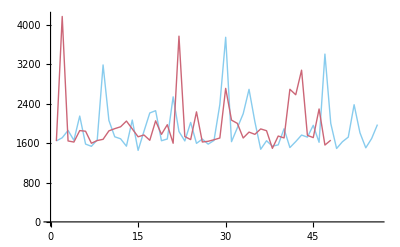

```mathematica
ListPlot[{Mean[binsc^2],Mean[binss^2]},Joined->True,PlotRange->All]
```

```mathematica
ListPlot[{Mean@T[binsc],Mean@T[binss]},Joined->True]
```

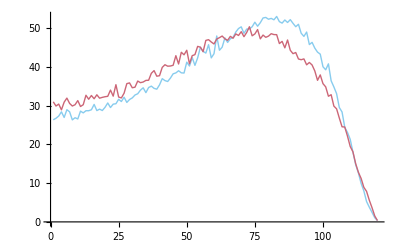

```mathematica
ListPlot[{Mean@T[binsc],Mean@T[binss]},Joined->True]
```

```mathematica
ListPlot[{Mean@T[binsc],Mean@T[binss]},Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
binsc=Import["weighteddegree_Control","Table"];binss=Import["weighteddegree_Schizo","Table"];
```

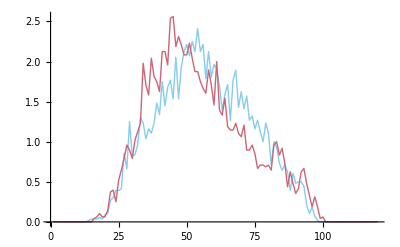

```mathematica
ListPlot[{Mean@T[binsc],Mean@T[binss]},Joined->True,PlotRange->All]
```

```mathematica
Export["data_params",Table["parameter_"<>ToString[ii],{ii,38}],"CSV"];
```

```mathematica
(* select only quantities bounded in [0,1] *)
(*selectedq=Flatten@Table[{1,3,5}+ii,{ii,{0,6,12,18}}];*)

fileselect="6"; (* "reduced" *)
categories={"healthy","schizo"};
categoryfiles={"data_con"<>fileselect,"data_schizo"<>fileselect};
numcategories=Length[categories];
origquantities=(Flatten@Import["data_params","CSV"]);
orignumquantities=Length@origquantities;

Do[tempdata=Import[categoryfiles[[ii]],"CSV"];
(*jm=Length[selectedq]/4;
(* transform 2nd moments to raw ones *)
Do[tempdata[[jj]]=Sqrt[tempdata[[jj]]+tempdata[[jj-jm]]^2],{jj,jm+1,2*jm}];
(* transform 3nd moments to raw ones *)
Do[tempdata[[jj]]=CubeRoot[tempdata[[jj]]+3*tempdata[[jj-jm]]^2*tempdata[[jj-2*jm]]-2*tempdata[[jj-2*jm]]^3],{jj,2*jm+1,3*jm}];
(* transform 4nd moments to raw ones *)
Do[tempdata[[jj]]=Surd[tempdata[[jj]]+4*tempdata[[jj-jm]]^3*tempdata[[jj-3*jm]]-6*tempdata[[jj-2*jm]]^2*tempdata[[jj-3*jm]]^2+3*tempdata[[jj-3*jm]]^4,4],{jj,3*jm+1,4*jm}];*)

origsubjectfile[ii]=N@tempdata;
numindividuals[ii]=Length[origsubjectfile[ii][[1]]],
{ii,numcategories}];
(* one row for each quantity, one column for each individual *)
minnumindividuals=Min@Table[numindividuals[ii],{ii,numcategories}];
```

```mathematica
AbsoluteTiming[len=Length@origsubjectfile[1];Do[If[aa<bb,plot=ListPlot[Table[T@origsubjectfile[ii][[{aa,bb},;;]],{ii,numcategories}],PlotRange->All(*{{0,All},{0,All}}*),PlotStyle->{bpurple,red},PlotMarkers->{{Style["*",Bold],10},{Style["o",Bold],10}},Frame->True,FrameTicks->True,FrameLabel->origquantities[[{aa,bb}]]];
expdfr["visualize_data\\expldata-"<>ToString[aa]<>"_"<>ToString[bb],plot];,Null];
,{aa,len-1},{bb,aa+1,len}]]
```

{315.143,Null}

```mathematica
(* analysis with beta distribution *)
```

```mathematica
beta[s_,a_,b_]=Assuming[0<s<1,FS@PDF[BetaDistribution[a,b],s]]
```

((1-s)^(-1+b) s^(-1+a))/Beta[a,b]

```mathematica
pparam[datum_,a_,b_]:=(a-1)*Total[Log[datum]]+(b-1)*Total[Log[1-datum]]-Length[datum]*Log[Beta[a,b]]
```

```mathematica
(* we approximate posterior by the maximum-likelihood distribution *)
ClearAll[fun];Do[
maxx[ii]=Table[
fun=pparam[origsubjectfile[ii][[jj]],a,b];
{a,b}/.(NMaximize[{fun,a>=0&&b>=0},{a,b}][[2]]),{jj,orignumquantities}];
,{ii,numcategories}]
```

```mathematica
logpred[cat_,datum_]:=Total[Table[Log@beta[datum[[ii]],maxx[cat][[ii,1]],maxx[cat][[ii,2]]],{ii,orignumquantities}]]
```

```mathematica
Exp@logpred[1,T[origsubjectfile[1]][[4]]]
```

452316.

```mathematica
Exp@logpred[1,T[origsubjectfile[2]][[1]]]
```

194012.

```mathematica
(pred1=Table[
Normalize[Table[Exp@logpred[ii,T[origsubjectfile[1]][[jj]]],{ii,numcategories}],Total]
,{jj,Length[T[origsubjectfile[1]]]}])*100//MF
```

(26.2894 | 73.7106
17.4678 | 82.5322
87.9017 | 12.0983
55.8919 | 44.1081
87.2399 | 12.7601
78.5038 | 21.4962
50.1355 | 49.8645
31.8067 | 68.1933
33.0628 | 66.9372
84.1268 | 15.8732
8.46744 | 91.5326
36.4935 | 63.5065
49.7025 | 50.2975
85.7756 | 14.2244
85.708 | 14.292
86.4282 | 13.5718
83.3834 | 16.6166
79.7317 | 20.2683
76.599 | 23.401
63.136 | 36.864
83.3319 | 16.6681
88.089 | 11.911
49.9164 | 50.0836
0.786243 | 99.2138
77.7921 | 22.2079
19.7703 | 80.2297
31.0499 | 68.9501
79.133 | 20.867
0.030935 | 99.9691
9.09555 | 90.9044
45.996 | 54.004
86.7137 | 13.2863
87.2703 | 12.7297
67.9995 | 32.0005
84.9199 | 15.0801
63.922 | 36.078
85.8818 | 14.1182
60.2775 | 39.7225
53.7634 | 46.2366
87.6911 | 12.3089
54.4062 | 45.5938
34.8138 | 65.1862
6.64431 | 93.3557
84.9928 | 15.0072
87.701 | 12.299
78.5018 | 21.4982
28.9939 | 71.0061
87.3921 | 12.6079
70.0337 | 29.9663
34.3006 | 65.6994
13.4317 | 86.5683
72.8133 | 27.1867
86.6531 | 13.3469
79.0629 | 20.9371
21.0357 | 78.9643
87.0101 | 12.9899)

```mathematica
Mean[pred1]
```

{0.589119,0.410881}

```mathematica
(pred2=Table[
Normalize[Table[Exp@logpred[ii,T[origsubjectfile[2]][[jj]]],{ii,numcategories}],Total]
,{jj,Length[T[origsubjectfile[2]]]}])*100//MF
```

(47.033 | 52.967
3.01796 | 96.982
17.3159 | 82.6841
71.5727 | 28.4273
3.36725 | 96.6328
2.81232 | 97.1877
42.609 | 57.391
60.7914 | 39.2086
83.1787 | 16.8213
4.05076 | 95.9492
67.9229 | 32.0771
82.6406 | 17.3594
88.0406 | 11.9594
88.1653 | 11.8347
7.23015 | 92.7699
11.5507 | 88.4493
63.8424 | 36.1576
0.588398 | 99.4116
85.0129 | 14.9871
86.8422 | 13.1578
84.4789 | 15.5211
13.3549 | 86.6451
73.3205 | 26.6795
32.8762 | 67.1238
85.2808 | 14.7192
56.8155 | 43.1845
63.7096 | 36.2904
27.6053 | 72.3947
39.8188 | 60.1812
30.2527 | 69.7473
87.8506 | 12.1494
0.751899 | 99.2481
79.0838 | 20.9162
5.37655 | 94.6235
7.50478 | 92.4952
1.95774 | 98.0423
86.7798 | 13.2202
66.3148 | 33.6852
79.9852 | 20.0148
13.7296 | 86.2704
73.2129 | 26.7871
71.0299 | 28.9701
64.9894 | 35.0106
7.95109 | 92.0489
86.3653 | 13.6347
79.1745 | 20.8255
65.1027 | 34.8973
30.8172 | 69.1828)

```mathematica
correct[a_]=Boole[a>0.5]
```

Boole[a>0.5]

```mathematica
spred1=Map[correct,pred1,{2}];spred2=Map[correct,pred2,{2}];
```

```mathematica
{Total[spred1],Total[spred2]}
```

{{36,20},{26,22}}

```mathematica
{Mean[pred1],Mean[pred2]}
```

{{0.589119,0.410881},{0.486057,0.513943}}

```mathematica
(* Now using graphweights1 only *)
```

```mathematica
(* select only quantities bounded in [0,1] *)
selectedq={1};

fileselect="3"; (* "reduced" *)
categories={"healthy","schizo"};
categoryfiles={"data_con"<>fileselect,"data_schizo"<>fileselect};
numcategories=Length[categories];
origquantities=(Flatten@Import["data_params","CSV"])[[selectedq]];
orignumquantities=Length@origquantities;

Do[tempdata=Import[categoryfiles[[ii]],"CSV"][[selectedq]];
(*jm=Length[selectedq]/4;
(* transform 2nd moments to raw ones *)
Do[tempdata[[jj]]=Sqrt[tempdata[[jj]]+tempdata[[jj-jm]]^2],{jj,jm+1,2*jm}];
(* transform 3nd moments to raw ones *)
Do[tempdata[[jj]]=CubeRoot[tempdata[[jj]]+3*tempdata[[jj-jm]]^2*tempdata[[jj-2*jm]]-2*tempdata[[jj-2*jm]]^3],{jj,2*jm+1,3*jm}];
(* transform 4nd moments to raw ones *)
Do[tempdata[[jj]]=Surd[tempdata[[jj]]+4*tempdata[[jj-jm]]^3*tempdata[[jj-3*jm]]-6*tempdata[[jj-2*jm]]^2*tempdata[[jj-3*jm]]^2+3*tempdata[[jj-3*jm]]^4,4],{jj,3*jm+1,4*jm}];*)

origsubjectfile[ii]=N@tempdata;
numindividuals[ii]=Length[origsubjectfile[ii][[1]]],
{ii,numcategories}];
(* one row for each quantity, one column for each individual *)
minnumindividuals=Min@Table[numindividuals[ii],{ii,numcategories}];
```

```mathematica
Do[If[aa<bb,plot=ListPlot[Table[T@origsubjectfile[ii][[{aa,bb},;;]],{ii,numcategories}],PlotRange->All(*{{0,All},{0,All}}*),PlotMarkers->{{Style["*",Bold],10},{Style["o",Bold],10}},Frame->True,FrameTicks->True,FrameLabel->origquantities[[{aa,bb}]]];
expng["visualize_data5\\expldata-"<>ToString[aa]<>"_"<>ToString[bb],plot];,Null];
,{aa,{1,4,10,16,22}},{bb,24}]
```

```mathematica
(* analysis with beta distribution *)
```

```mathematica
beta[s_,a_,b_]=Assuming[0<s<1,FS@PDF[BetaDistribution[a,b],s]]
```

((1-s)^(-1+b) s^(-1+a))/Beta[a,b]

```mathematica
pparam[datum_,a_,b_]:=(a-1)*Total[Log[datum]]+(b-1)*Total[Log[1-datum]]-Length[datum]*Log[Beta[a,b]]
```

```mathematica
(* we approximate posterior by the maximum-likelihood distribution *)
ClearAll[fun];Do[
maxx[ii]=Table[
fun=pparam[origsubjectfile[ii][[jj]],a,b];
{a,b}/.(NMaximize[{fun,a>=0&&b>=0},{a,b}][[2]]),{jj,orignumquantities}];
,{ii,numcategories}]
```

```mathematica
logpred[cat_,datum_]:=Total[Table[Log@beta[datum[[ii]],maxx[cat][[ii,1]],maxx[cat][[ii,2]]],{ii,orignumquantities}]]
```

```mathematica
Exp@logpred[1,T[origsubjectfile[1]][[4]]]
```

3.58615

```mathematica
Exp@logpred[1,T[origsubjectfile[2]][[1]]]
```

3.29095

```mathematica
(pred1b=Table[
Normalize[Table[Exp@logpred[ii,T[origsubjectfile[1]][[jj]]],{ii,numcategories}],Total]
,{jj,Length[T[origsubjectfile[1]]]}])*100//MF
```

(48.3484 | 51.6516
46.3614 | 53.6386
54.5942 | 45.4058
50.5387 | 49.4613
54.5065 | 45.4935
52.5062 | 47.4938
50.576 | 49.424
48.4762 | 51.5238
45.2721 | 54.7279
53.6486 | 46.3514
46.3529 | 53.6471
48.4199 | 51.5801
50.6049 | 49.3951
53.6132 | 46.3868
54.6218 | 45.3782
54.0833 | 45.9167
53.4506 | 46.5494
52.4686 | 47.5314
52.9737 | 47.0263
50.9749 | 49.0251
53.264 | 46.736
54.5541 | 45.4459
49.8131 | 50.1869
41.6503 | 58.3497
52.7125 | 47.2875
48.3498 | 51.6502
49.8164 | 50.1836
52.9432 | 47.0568
36.9 | 63.1
38.4483 | 61.5517
49.8259 | 50.1741
54.1534 | 45.8466
54.4046 | 45.5954
50.7428 | 49.2572
53.642 | 46.358
52.4464 | 47.5536
54.1357 | 45.8643
51.5846 | 48.4154
50.7994 | 49.2006
54.4925 | 45.5075
51.3228 | 48.6772
48.922 | 51.078
45.4376 | 54.5624
53.7618 | 46.2382
54.4676 | 45.5324
52.7421 | 47.2579
44.5135 | 55.4865
54.3271 | 45.6729
53.3037 | 46.6963
49.0082 | 50.9918
45.973 | 54.027
50.8316 | 49.1684
54.4283 | 45.5717
53.542 | 46.458
47.5292 | 52.4708
54.1441 | 45.8559)

```mathematica
Mean[pred1b]
```

{0.50738,0.49262}

```mathematica
(pred2b=Table[
Normalize[Table[Exp@logpred[ii,T[origsubjectfile[2]][[jj]]],{ii,numcategories}],Total]
,{jj,Length[T[origsubjectfile[2]]]}])*100//MF
```

(49.6125 | 50.3875
35.4769 | 64.5231
49.1748 | 50.8252
52.0389 | 47.9611
43.2237 | 56.7763
43.4719 | 56.5281
49.7403 | 50.2597
50.0327 | 49.9673
53.5351 | 46.4649
42.9363 | 57.0637
50.2986 | 49.7014
52.8351 | 47.1649
54.5614 | 45.4386
54.5957 | 45.4043
46.4196 | 53.5804
45.5291 | 54.4709
51.1563 | 48.8437
40.0767 | 59.9233
53.9387 | 46.0613
54.2278 | 45.7722
54.2189 | 45.7811
40.61 | 59.39
51.6166 | 48.3834
48.4128 | 51.5872
53.9691 | 46.0309
50.1386 | 49.8614
51.1031 | 48.8969
47.9819 | 52.0181
48.5044 | 51.4956
43.5522 | 56.4478
54.5711 | 45.4289
42.6917 | 57.3083
52.721 | 47.279
43.7713 | 56.2287
45.6395 | 54.3605
43.6624 | 56.3376
54.3651 | 45.6349
52.8733 | 47.1267
53.4602 | 46.5398
46.1582 | 53.8418
51.4046 | 48.5954
51.1014 | 48.8986
49.8863 | 50.1137
45.2388 | 54.7612
54.274 | 45.726
52.0787 | 47.9213
51.4249 | 48.5751
48.6522 | 51.3478)

```mathematica
correct[a_]=Boole[a>0.5]
```

Boole[a>0.5]

```mathematica
spred1b=Map[correct,pred1b,{2}];spred2b=Map[correct,pred2b,{2}];
```

```mathematica
{Total[spred1b],Total[spred2b]}
```

{{37,19},{25,23}}

```mathematica
{Mean[pred1b],Mean[pred2b]}
```

{{0.50738,0.49262},{0.491034,0.508966}}

```mathematica
{Total[spred1],Total[spred2]}
```

{{37,19},{26,22}}

```mathematica
{Mean[pred1],Mean[pred2]}
```

{{0.597315,0.402685},{0.481633,0.518367}}